# 5 A realization of {5/2,3,5}

The following text and figures are as in section 5 of the thesis.

In this section we construct in a somewhat unexpected way the regular star 4-polytope {5/2,3,5} , within which we later find a chiral 4-polytope.

Our starting point is the regular convex 4-polytope {3,3,5}. The construction is based on the observation that, in the same way as the false vertices of a pentagram form a pentagon, the false vertices of a great stellated dodecahedron {5/2,3} form an icosahedron {3,5} (fig. 1).

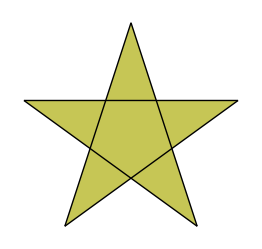
-Graphics--Graphics3D-

(a) In {5/2}.					(b) In {5/2,3}.

Fig. 1: Polytopes of false vertices

This icosahedron is thought to be the vertex figure of some vertex in {3,3,5}, so that its center and its vertices represent some vertices of {3,3,5}. We choose a basic flag for this icosahedron, which determines the generating reflections R_0 to R_3 of its symmetry group. Then we choose a base flag in the surrounding {5/2,3}, which determines reflections P_0 to P_3. We may express the P_i in terms of the R_i. Acting with the group generated by the P_i on the base flag of  {5/2,3} yields {5/2,3,5}.

## 5.1 3-dimensional analogue

For better understanding, we start by presenting the 3-dimensional analogue of our argument. Take the pentagon of false-vertices of the pentagram to be the vertex-figure of some vertex in a regular icosahedron {3,5}, and choose a base flag for the icosahedron. We represent such flag by the basic tetrahedron given by the base vertex and the centroids of the base edge, the base face and the icosahedron (fig 2b). To it corresponds a triangle shown in fig 2a.

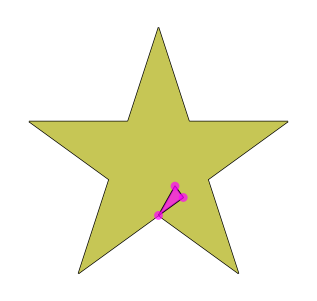
-Graphics--Graphics3D-

(a) Seen in {5/2}					(b) Seen in {3,5}

Fig. 2: Base flag of {3,5}.

We denote reflections and their mirrors with the same symbol. Let R_i for i=0,1,2 be reflections on the sides of the triangle in fig 2a in the following way: R_0 goes through the blue and green vertex, R_1 through the red and blue, and R_2 through the red and green. Notice these lines correspond to planes through the origin in fig. 2b, so that the R_i may be thought as plane reflections.

Now choose a flag for the pentagram in the 2-dimensional picture as represented in fig 3a.

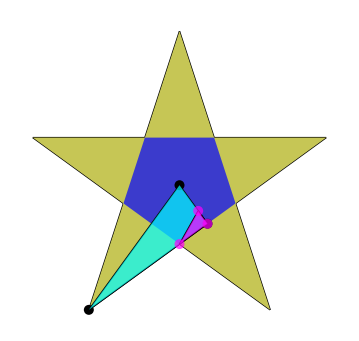
-Graphics--Graphics3D-

(a) Seen in   {5/2}					(b) Seen in   {3,5}

Fig. 3: Base flag of {5/2}.

We define the reflections P_i in terms of the R_i as follows:

P_0=R_0,   P_1=R_1 R_2 R_1 R_0 R_1 R_2 R_1, and   P_2=R_2

P_1 is just R_0 conjugated by the reflection through the vertical line in the center of the picture.

If the group ⟨P_0,P_1,P_2⟩ is a C-string group, then it is an abstract polytope, and finding a geometric flag by Wythoff’s construction amounts to finding a vertex fixed by P_1 and P_2 but not by P_0. For the natural choice of base vertex in our construction, we obtain a the base flag shown in fig. 3b.

Like before, we may think the P_i are plane reflections. Acting with the group generated by the P_i on this flag produces {5/2,5}, a regular star polyhedron with the same vertex-set as the icosahedron fig. 4.

-Graphics3D-

Fig. 4: {5/2,5}.

## 5.2 Construction of {5/2,3,5} from {3,3,5}

Now we take the icosahedron of false vertices within {5/2,3} to be the vertex-figure of some vertex in {3,3,5}, and we choose a base flag for {3,3,5}. Recall the cells of {3,3,5} are tetrahedra, and notice our choice of base flag does not contain the vertex of which {3,5} is thought to be the vertex-figure (Figs. 5a and 5b).

-Graphics3D--Graphics3D-

(a) In   {3,5}					(b) In the base cell

Fig. 5: Base flag of {3,3,5}.

And now choose a base flag for {5/2,3} (figs. 6a and 6b).

-Graphics3D-

(a) In the base cell of {3,3,5}.

-Graphics3D-

(b) In {5/2,3}. Edges in the base of {5/2,3} are highlighted.

Fig. 6. Base flags of  {3,3,5} and {5/2,3}.

We may define the generating reflections of the symmetry group of {3,3,5} using its base flag as follows. Define the red vertex as v_0, the blue v_1, the green v_2 and the yellow v_3. The mirror of the reflection R_i is the plane through all but v_i (as an example we show R_0 in fig 7).

-Graphics3D-

Fig. 7: R_0.

Recall we think of these as hyperplane reflections, each determined by three vertices in the base flag and the origin in 4-space.

Now we may define the generating reflections for the symmetry group of {5/2,3,5} in terms of the R_i (fig. 8).

-Graphics3D-

(a) P_0=R_0.

-Graphics3D-

(b) P_1=R_1 R_2 R_3 R_2 R_1 R_0 R_1 R_2 R_3 R_2 R_1.

-Graphics3D-

(a) P_2=R_3.

-Graphics3D-

(a) P_3=R_2.

Fig. 8: The P_i in terms of the R_i.

P_1 is just R_0 conjugated by R_1 R_2 R_3 R_2 R_1 (figs. 9a and 9b).

-Graphics3D-

(a) R_0 conjugated by R_1 R_2 R_3 R_2 R_1.

-Graphics3D-

(b) Showing the base flag of {5/2,3}.

Fig 9. P_1.

It has been confirmed in abstract.txt that ⟨P_0,P_1,P_2,P_3⟩ is a C-string group (see Appendix A.1). Specifically,

P_i^2=(P_0 P_2)^2=(P_0 P_3)^2=(P_1 P_3)^2=(P_0 P_1)^5=(P_1 P_2)^3=(P_2 P_3)^5=Id

for all i, and the intersection property holds (see int-prop.txt).

-Graphics3D-

(a) As we’ve been picturing it.

-Graphics3D-

(b) Stereographic projection

Fig 10. Base flag of {5/2,3,5}.

To produce a realization we must find a vertex fixed by P_1, P_2 and P_3 but not by P_0. The natural choice is shown in fig. 10, and it is defined as follows. First we take v_0 to the opposite vertex of the base face in the base tetrahedron using R_0 R_1 R_2. Next we rotate twice about the base edge conjugated by R_1 R_2 R_3 R_2 R_1.

So let

w_0=v_0 R_0 R_1 R_2 · R_1 R_2 R_3 R_2 R_1 · R_3 R_2 R_3 R_2 · R_1 R_2 R_3 R_2 R_1

(we use dots to facilitate lecture), which is, in effect, fixed by all the P_i but P_0 (see geometric.txt, Appendix A1.2). We have also shown that   ⟨R_0,R_1,R_2,R_3⟩=⟨P_0,P_1,P_2,P_3⟩, so that the vertex-set in both structures is the same (this equality also follows from thm. 7D13, [6]). It follows that the realization is symmetric. Faithfulness was proved by comparing the number of i-faces in abstract.txt, and geometric.txt.

Since the R_i are hyperplane reflections, we have a classical polytope as defined in Section 3.2 (see [15]). The only such polytopes in 𝔼^4 arising from the regular abstract polytope {5,3,5} are the star 4-polytopes {5/2,3,5} and {5,3,5/2} (thm. 7D13 [6]). However, the rotation about the edge in this polytope is the reverse of that of {3,3,5}, so it cannot be of type 5/2. This completes the proof that we have constructed {5/2,3,5}.

-Graphics3D-

(a) The base face

-Graphics3D-

(b) The base cell

Fig 10. Stereographic projections of {5/2,3,5}.

# 6 A chiral 4-polytope from {5/2,3,5}

For the following two sections only the figures are included. More pictures may be found at Section-5C.nb and Section-6A.nb.

-Graphics3D-

Fig 12. Stereographic projection of the base face of {12/(1,5),3,5}. We also show the base face and flag of {5/2,3,5}.

# 7 A chiral 4-polytope from {5,3,5/2}

-Graphics3D-

(a) The base face. We also show the base face and flag of {5,3,5/2}.

-Graphics3D-

(b) Five faces at the edge. We show part of the surface spanned between the edge and the axis of twist in every face.

Fig 13. Stereographic projection of the base face of {12/(1,5),3,5/2}.